```mathematica
(*
ScaledDirectory is the location of the scaled files. FinalDirectory is where your files will be saved. 
You will have to change these to your directories.
You will have to create the final directory folder for the output files.
*)
voltage =250;
DataDirectory=StringJoin["C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-14 Voltage\\",ToString[voltage]];
SetDirectory[DataDirectory];
SaveDirectory ="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-14 Voltage\\fit_result";
fnup=FileNames["scanup*"]
fndown=FileNames["scandown*"]
```

{scanup01.txt,scanup02.txt,scanup03.txt,scanup04.txt}

{scandown01.txt,scandown02.txt,scandown03.txt,scandown04.txt}

```mathematica
Clear[AES,BES,Ae153,Be153];
Clear[aArray,f0,gArray];
L[f_]=aArray/(1+4 (f-f0)^2/gArray^2);
transitions=Join[Transpose[sorted151],Transpose[sorted153]];
transitions = Select[transitions,Abs[#[[3]]]<4&];
```

```mathematica
f0=transitions[[All,4]];
aArrayguess=Table[{ToExpression["a"<>If[i<10,"0"<>ToString[i],ToString[i]]],If[i≤Floor[Length[transitions]/2],0.1,0.02]},{i,1,Length[f0]}];
aArray=aArrayguess[[All,1]];
gArrayguess = Table[{ToExpression["γ"<>If[i<10,"0"<>ToString[i],ToString[i]]],20},{i,1,Length[f0]}];
gArray=gArrayguess[[All,1]];
Clear[AGS,BGS,AES,BES,Ae153,Be153];
AGS=-20.0523;BGS=-0.7012;
Ag=AGS;
Bg =BGS;
Ag153 =Ag153m;
Bg153 =Bg153m;
(*AES=Ae9Halvesm;
BES=Be9Halvesm;
Ae153=Ae153m;
Be153=Be153m;*)
fcogGuess = 3620;
tofit[f_]=Tr[L[f]]+off+m (f-fcog);
```

```mathematica
fitcheck[in_]:=Module[{},
nlm=NonlinearModelFit[in,tofit[f],var,f];
(*nlm["AdjustedRSquared"]*)
Be153/.nlm["BestFitParameters"]
];
```

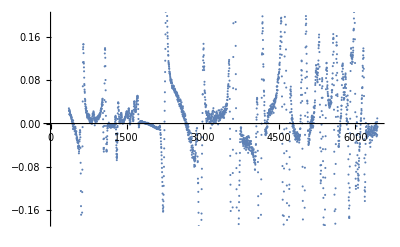

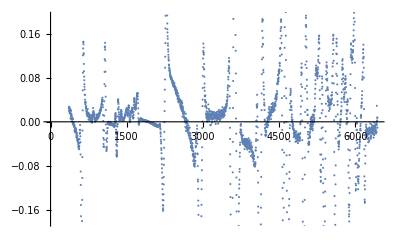

```mathematica
dataup=Drop[Import["scanup01.txt","Table"][[All,{1,3}]],150];
ListPlot[dataup]
datadown=Drop[Import["scandown01.txt","Table"][[All,{1,3}]],150];
ListPlot[datadown]
```

```mathematica
testup ={};
testdown={};
guess =4075;
scale =0.2;
For[i=-5, i≤5,i++,
dev = scale*i;
var=Join[aArrayguess2,gArrayguess,{{fcog,guess+dev},{off,0.01},{m,0},{nu,-2977},{Ae153,Ae153m},{Be153,Be153m},{AES,Ae9Halvesm},{BES,Be9Halvesm}}];
rsquaredup=fitcheck[dataup];
(*rsquareddown=fitcheck[datadown];*)
AppendTo[testup,rsquaredup];
(*AppendTo[testdown,rsquareddown];*)
Print[i]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-5

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-4

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

-3

-2

-1

0

1

2

3

4

5

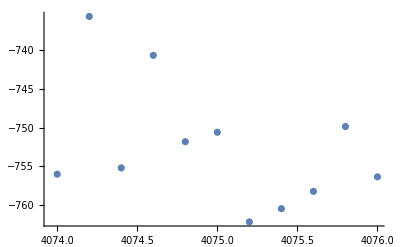

```mathematica
tab = Table[guess+scale*n,{n,-5,5,1}];
ListPlot[{Transpose[{tab,testup}](*,Transpose[{tab,testdown}]}*)},PlotRange->All]
```

```mathematica
testup
```

{0.962097,0.96544,0.972345,0.996135,0.996992,0.997087,0.997118,0.997414,0.997197,0.982091,0.974051}

{{{4030,4030},{4040,4040},{4050,4050},{4060,4060},{4070,4070},{4080,4080},{4090,4090},{4100,4100},{4110,4110},{4120,4120},{4130,4130}},{{-219.749,-801.594},{-219.64,-633.355},{-215.75,-651.666},{-218.51,-699.079},{-218.548,-747.803},{-218.616,-735.004},{-218.598,-737.795},{-218.609,-736.166},{-218.651,-732.082},{-219.572,-668.921},{-216.876,-759.557}}}

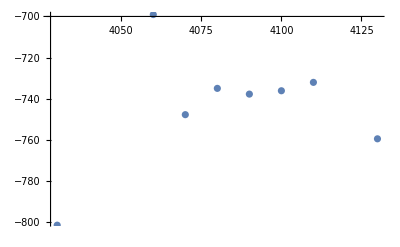

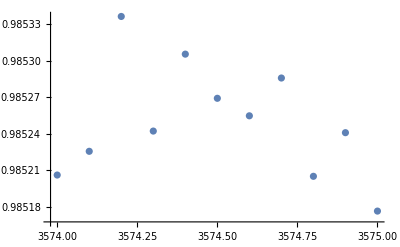

-Graphics-

```mathematica
aArrayVal=aArray/.nlm["BestFitParameters"];
aArrayguess2 = Transpose[{aArray,aArrayVal}];
```

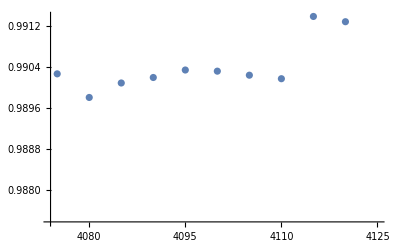

```mathematica
ListPlot[Transpose[{tab,testup}]]
```

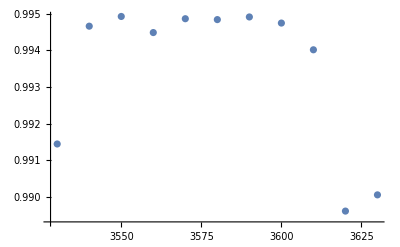

-Graphics-

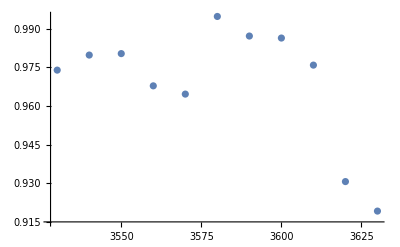

-Graphics-

```mathematica
testtot ={};
```

```mathematica
testtot=Join[testtot,Transpose[{tab,test}]];
```

Transpose::nmtx: The first two levels of {{4075,4080,4085,4090,4095,4100,4105,4110,4115,4120,«1»},test} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

```mathematica
ListPlot[testtot,PlotRange->{{3560,3580},{.98,1}}]
```

Transpose::nmtx: The first two levels of {{4075.,4080.,4085.,4090.,4095.,4100.,4105.,4110.,4115.,4120.,«1»},test} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::nmtx: The first two levels of {{4075.,4080.,4085.,4090.,4095.,4100.,4105.,4110.,4115.,4120.,«1»},test} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::nmtx: The first two levels of {{4075.,4080.,4085.,4090.,4095.,4100.,4105.,4110.,4115.,4120.,«1»},test} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

ListPlot::lpn: Join[{},Transpose[{{4075.,4080.,4085.,4090.,4095.,4100.,4105.,4110.,4115.,4120.,«1»},test}]] is not a list of numbers or pairs of numbers.

ListPlot[Join[{},Transpose[{{4075,4080,4085,4090,4095,4100,4105,4110,4115,4120,4125},test}]],PlotRange→{{3560,3580},{0.98,1}}]